# Rossler

The previous notebook implemented Rossler + sensitivities on the vertical section  Σ^-={y_1=c,-y_2-y_3<0}⊂ℝ^3.  The plan is to use these tools to find periodic orbits for a range of values for c.   We have seen a single once around periodic orbit for c small, a single twice around orbit for c slightly larger and a bunch of “almost periodic orbits” for c larger.

### Rossler return map and gradient: Function Section Σ^-={y_1=c,-y_2-y_3<0}⊂ℝ^3!

A once around orbit satisfies q=p(q).  In words, a once around orbit is a fixed point of the forward poincare map p.  Here is our omnibus function for the return time τ, first return map p, and full fixed-time sensitivity J.

```mathematica
Clear[f,dyf,ReturnMapAndTimeAndJ]
f[{a_,b_,c_}][{x_,y_,z_}]:={-y-z,x + a y,b + z(x-c)}
dyf[{a_,b_,c_}][{x_,y_,z_}]:=({{0, -1, -1}, {1, a, 0}, {z, 0, x-c}}) 
ReturnMapAndTimeAndJ[{a_,b_,c_},{f_,dyf_}][{u1_,u2_}]:= Module[{y0,TMin=0.001,TMax=123,
tVal,yVal,JVal,ySol,JSol,y,J,t},
y0={c,u1,u2};
{tVal,yVal,JVal} = Reap[
{ySol,JSol}= NDSolveValue[ {
y'[t]==f[{a,b,c}][y[t]],
J'[t]==dyf[{a,b,c}][y[t]].J[t],
y[0]==y0,J[0]==IdentityMatrix[3],
WhenEvent[Indexed[y[t],1]-c <0,If[t>TMin, Sow[{t,y[t],J[t]}]; "StopIntegration"]]
(* I have no idea why I had to use indexed instead of [[]] in here! *)
},{y,J},{t,0,TMax}];
]⟦2,1,1⟧
]
```

We are looking for Fixed Points

```mathematica
{a,b,c}={0.2,0.2,2.6};
FixedPointSweep=Table[
{t,p,J}=ReturnMapAndTimeAndJ[{a,b,c},{f,dyf}][{u1,u2}];
p-{c,u1,u2},
{u1,1,5,0.25},
{u2,0,4,0.25}];
TabView[{
"p_1-u_1 & p_2-u_2"->Show[
ListContourPlot[FixedPointSweep⟦All,All,2⟧,
Contours->{-0.5,0,0.5},
DataRange->{{1,5},{0,4}},
ContourStyle->Red,ContourLabels->True,ContourShading->False],
ListContourPlot[FixedPointSweep⟦All,All,3⟧,
Contours->{-0.5,0,0.5},
DataRange->{{1,5},{0,4}},
ContourStyle->Blue,ContourLabels->True,ContourShading->False]
],
"||p-u||"->ListContourPlot[
Map[Norm,FixedPointSweep⟦All,All,2;;3⟧,{2}],
Contours->25,
DataRange->{{1,5},{0,4}},
ContourLabels->True]
}]
```

12

To find the fixed point accurately I need to derivative in the surface accounting for the change in the return time.  We worked this all out for the vertical section y_1=c.  All we have to do is implement the operations from the slides.  The recipe form the slides is 
	Dp(u_1,u_2) | = | (J_22 | J_23
J_32 | J_33)+1/(p_1+p_2)((c+a p_1)J_12 | (c+a p_1)J_13
b J_12 | b J_13)  
The first term is full sensitivity restricted to the y_2 (aka u_1) and y_3 (aka u_2) plane.  The second term is the correction due to the variation in the return time.  I am going to make a new function that returns the updated position and this gradient.

```mathematica
pAndDp[{a_,b_,c_},{f_,dyf_}][{u1_,u2_}]:= Module[{t,p,J,Dp},
{t,p,J}=ReturnMapAndTimeAndJ[{a,b,c},{f,dyf}][{u1,u2}];
Print[t,p];
Dp=({{J⟦2,2⟧, J⟦2,3⟧}, {J⟦3,2⟧, J⟦3,3⟧}})+1/(p⟦2⟧+p⟦3⟧)({{(c+ a p⟦2⟧)J⟦1,2⟧, (c+ a p⟦2⟧)J⟦1,3⟧}, {b J⟦1,2⟧, b J⟦1,3⟧}});
{p⟦2;;3⟧,Dp}
]
```

Lots of complicated Calculus III chain rule computations went into this formula.  We need to check we did not mess up!

```mathematica
{a,b,c}={0.2,0.2,2.6};
u0={4.3,1.3};
{p0, Dp0}= pAndDp[{a,b,c},{f,dyf}][u0]
ReturnMapAndTimeAndJ[{a,b,c},{f,dyf}][u0]
```

5.38731{2.6,-0.235604,18.2303}

{{-0.235604,18.2303},{{-1.39433,0.209308},{8.28938,-1.24436}}}

```mathematica
Clear[t]
ySol=NDSolveValue[{y'[t]==f[{a,b,c}][y[t]],y[0]=={c,1.3,4.3}},y,{t,0, 12}]
ParametricPlot3D[ySol[t],{t,0, 12},PlotRange->All]
```

InterpolatingFunction[…]

-Graphics3D-

```mathematica
LinApp[u_]:=(p0-u0)+(Dp0-IdentityMatrix[2]).(u-u0)
```

{{-0.235604,18.2303},{{-1.39433,0.209308},{8.28938,-1.24436}}}

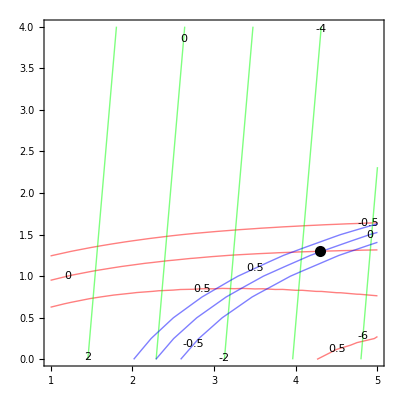

```mathematica
Show[
ListContourPlot[FixedPointSweep⟦All,All,2⟧,
Contours->{-0.5,0,0.5},
DataRange->{{1,5},{0,4}},
ContourStyle->Red,ContourLabels->True,ContourShading->False],
ContourPlot[ LinApp[{u1,u2}]⟦1⟧,
{u1,1,5},{u2,0,4},
ContourShading->False,
ContourStyle->Green, ContourLabels->True],
ListContourPlot[FixedPointSweep⟦All,All,3⟧,
Contours->{-0.5,0,0.5},
DataRange->{{1,5},{0,4}},
ContourStyle->Blue,ContourLabels->True,ContourShading->False],
Epilog->{PointSize[0.02],Point[u0]}
]
```